Метод на разполовяването

Условия за намиране на корен на уравнението f (x) = 0  с точност ε:
          1. Функцията f(x) да е непрекъсната в интервала [a, b];
          2. За интервала [a, b] да е изпълнено условието f(a).f(b) < 0.
стоп критерий: (b-a)/2^n<ε.

Задача 1. По метода на разполовяването да се намери коренът на уравнението
 sin(x)-x+0,15=0 с точност ε = 10^-4.

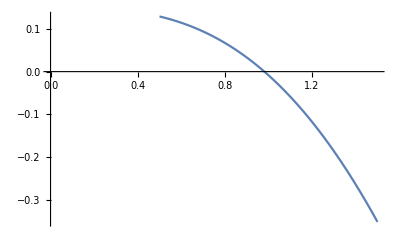

```mathematica
(* дефинираме функцията *)
f[x_]:=Sin[x]-x+0.15
Plot[f[x],{x,0.5,1.5},AxesOrigin->{0,0}]
```

```mathematica
(* Локализация на корена *)
a=0.5;b=1.5; 
 (* Задаване на точност *)
eps=10^-3;
(* Проверка за интервала *)
If [f[a]*f[b]>0,Print["Лош интервал!"];];
n=0; (* брой на итерациите *)
While[Abs[(b-a)/2]>eps,
c=(a+b)/2;(* делим интервала на две *)
Print["n = ",n,", a = ",a,"(",Style[Sign[f[a]],Red,Bold],"), b = ",b,"(",Style[Sign[f[b]],Red,Bold],"), c = ",c,"(",Style[Sign[f[c]],Red,Bold],"), err = ",(b-a)/2];
If[f[a]*f[c]<0,b=c,a=c];
Print["Следващият интервал е: [",a,", ", b,"]"];
n=n+1;
Print["---------------------------"];
];
c=(a+b)/2;
Print["n = ",n,", a = ",a,"(",Style[Sign[f[a]],Red,Bold],"), b = ",b,"(",Style[Sign[f[b]],Red,Bold],"), c = ",c,"(",Style[Sign[f[c]],Red,Bold],"), err = ",(b-a)/2];
Print[Style["Последно приближение: ",14,Red,Bold], Style[c,14,Red,Bold],Style[" с грешка ",14,Red,Bold],Style[(b-a)/2,14,Red,Bold]];
```

n = 0, a = 0.5(1), b = 1.5(-1), c = 1.(-1), err = 0.5

Следващият интервал е: [0.5, 1.]

---------------------------

n = 1, a = 0.5(1), b = 1.(-1), c = 0.75(1), err = 0.25

Следващият интервал е: [0.75, 1.]

---------------------------

n = 2, a = 0.75(1), b = 1.(-1), c = 0.875(1), err = 0.125

Следващият интервал е: [0.875, 1.]

---------------------------

n = 3, a = 0.875(1), b = 1.(-1), c = 0.9375(1), err = 0.0625

Следващият интервал е: [0.9375, 1.]

---------------------------

n = 4, a = 0.9375(1), b = 1.(-1), c = 0.96875(1), err = 0.03125

Следващият интервал е: [0.96875, 1.]

---------------------------

n = 5, a = 0.96875(1), b = 1.(-1), c = 0.984375(-1), err = 0.015625

Следващият интервал е: [0.96875, 0.984375]

---------------------------

n = 6, a = 0.96875(1), b = 0.984375(-1), c = 0.976563(1), err = 0.0078125

Следващият интервал е: [0.976563, 0.984375]

---------------------------

n = 7, a = 0.976563(1), b = 0.984375(-1), c = 0.980469(1), err = 0.00390625

Следващият интервал е: [0.980469, 0.984375]

---------------------------

n = 8, a = 0.980469(1), b = 0.984375(-1), c = 0.982422(-1), err = 0.00195313

Следващият интервал е: [0.980469, 0.982422]

---------------------------

n = 9, a = 0.980469(1), b = 0.982422(-1), c = 0.981445(-1), err = 0.000976563

Последно приближение: 0.981445 с грешка 0.000976563

Задача 2
По метода на разполовяването да се намери най-малкият корен на уравнението xcosx=ln(x) с точност 10^-5.

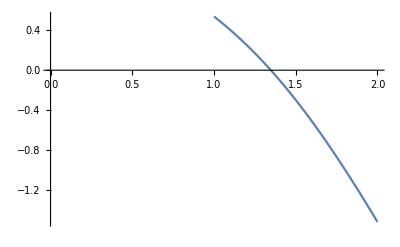

```mathematica
f[x_]:=x*Cos[x]-Log[x]
Plot[f[x],{x,1,2},AxesOrigin->{0,0}]
```

```mathematica
(* Локализация на корена *)
a=1.;b=2.; 
 (* Задаване на точност *)
eps=10^-5;
(* Проверка за интервала *)
If [f[a]*f[b]>0,Print["Лош интервал!"];];
n=0; (* брой на итерациите *)
While[Abs[(b-a)/2]>eps,
c=(a+b)/2;(* делим интервала на две *)
Print["n = ",n,", a = ",a,"(",Style[Sign[f[a]],Red,Bold],"), b = ",b,"(",Style[Sign[f[b]],Red,Bold],"), c = ",c,"(",Style[Sign[f[c]],Red,Bold],"), err = ",(b-a)/2];
If[f[a]*f[c]<0,b=c,a=c];
Print["Следващият интервал е: [",a,", ", b,"]"];
n=n+1;
Print["---------------------------"];
];
c=(a+b)/2;
Print["n = ",n,", a = ",a,"(",Style[Sign[f[a]],Red,Bold],"), b = ",b,"(",Style[Sign[f[b]],Red,Bold],"), c = ",c,"(",Style[Sign[f[c]],Red,Bold],"), err = ",(b-a)/2];
Print[Style["Последно приближение: ",14,Red,Bold], Style[c,14,Red,Bold],Style[" с грешка ",14,Red,Bold],Style[(b-a)/2,14,Red,Bold]];
```

n = 0, a = 1.(1), b = 2.(-1), c = 1.5(-1), err = 0.5

Следващият интервал е: [1., 1.5]

---------------------------

n = 1, a = 1.(1), b = 1.5(-1), c = 1.25(1), err = 0.25

Следващият интервал е: [1.25, 1.5]

---------------------------

n = 2, a = 1.25(1), b = 1.5(-1), c = 1.375(-1), err = 0.125

Следващият интервал е: [1.25, 1.375]

---------------------------

n = 3, a = 1.25(1), b = 1.375(-1), c = 1.3125(1), err = 0.0625

Следващият интервал е: [1.3125, 1.375]

---------------------------

n = 4, a = 1.3125(1), b = 1.375(-1), c = 1.34375(1), err = 0.03125

Следващият интервал е: [1.34375, 1.375]

---------------------------

n = 5, a = 1.34375(1), b = 1.375(-1), c = 1.35938(-1), err = 0.015625

Следващият интервал е: [1.34375, 1.35938]

---------------------------

n = 6, a = 1.34375(1), b = 1.35938(-1), c = 1.35156(-1), err = 0.0078125

Следващият интервал е: [1.34375, 1.35156]

---------------------------

n = 7, a = 1.34375(1), b = 1.35156(-1), c = 1.34766(-1), err = 0.00390625

Следващият интервал е: [1.34375, 1.34766]

---------------------------

n = 8, a = 1.34375(1), b = 1.34766(-1), c = 1.3457(1), err = 0.00195313

Следващият интервал е: [1.3457, 1.34766]

---------------------------

n = 9, a = 1.3457(1), b = 1.34766(-1), c = 1.34668(1), err = 0.000976563

Следващият интервал е: [1.34668, 1.34766]

---------------------------

n = 10, a = 1.34668(1), b = 1.34766(-1), c = 1.34717(1), err = 0.000488281

Следващият интервал е: [1.34717, 1.34766]

---------------------------

n = 11, a = 1.34717(1), b = 1.34766(-1), c = 1.34741(1), err = 0.000244141

Следващият интервал е: [1.34741, 1.34766]

---------------------------

n = 12, a = 1.34741(1), b = 1.34766(-1), c = 1.34753(1), err = 0.00012207

Следващият интервал е: [1.34753, 1.34766]

---------------------------

n = 13, a = 1.34753(1), b = 1.34766(-1), c = 1.3476(-1), err = 0.0000610352

Следващият интервал е: [1.34753, 1.3476]

---------------------------

n = 14, a = 1.34753(1), b = 1.3476(-1), c = 1.34756(1), err = 0.0000305176

Следващият интервал е: [1.34756, 1.3476]

---------------------------

n = 15, a = 1.34756(1), b = 1.3476(-1), c = 1.34758(-1), err = 0.0000152588

Следващият интервал е: [1.34756, 1.34758]

---------------------------

n = 16, a = 1.34756(1), b = 1.34758(-1), c = 1.34757(1), err = 7.62939×10^-6

Последно приближение: 1.34757 с грешка 7.62939×10^-6

Задача 3
По метода на разполовяването да се намери абсцисата на втората пресечната точка на графиката на функциите  f(x) = x^2/4 и g(x)=sinx, с точност 10^-4.

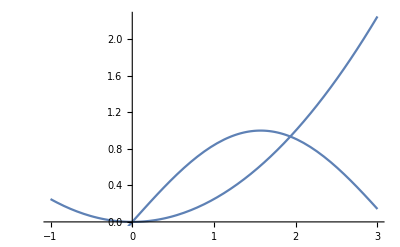

```mathematica
c=-1;d=3;
Show[Plot[x^2/4,{x,c,d},AxesOrigin->{0,0}],Plot[Sin[x],{x,c,d},AxesOrigin->{0,0}]]
```

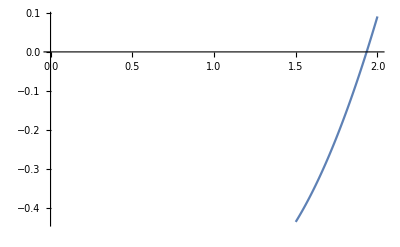

```mathematica
(* дефинираме функцията *)
Clear[x,f]
f[x_]:=x^2/4-Sin[x]
Plot[f[x],{x,1.5,2},AxesOrigin->{0,0}]
```

```mathematica
(* Локализация на корена *)
a=1.5;b=2.; 
 (* Задаване на точност *)
eps=10^-3;
(* Проверка за интервала *)
If [f[a]*f[b]>0,Print["Лош интервал!"];];
i=0; (* брой на итерациите *)
While[Abs[(b-a)/2]>eps,
c=(a+b)/2;(* делим интервала на две *)
Print["i = ",i,", a = ",a,"(",Style[Sign[f[a]],Red,Bold],"), b = ",b,"(",Style[Sign[f[b]],Red,Bold],"), c = ",c,"(",Style[Sign[f[c]],Red,Bold],"), err = ",(b-a)/2];
If[f[a]*f[c]<0,b=c,a=c];
Print["Следващият интервал е: [",a,", ", b,"]"];
i=i+1;
Print["---------------------------"];
];
c=(a+b)/2;
Print["i = ",i,", a = ",a,"(",Style[Sign[f[a]],Red,Bold],"), b = ",b,"(",Style[Sign[f[b]],Red,Bold],"), c = ",c,"(",Style[Sign[f[c]],Red,Bold],"), err = ",(b-a)/2];
Print[Style["Последно приближение: ",14,Red,Bold], Style[c,14,Red,Bold],Style[" с грешка ",14,Red,Bold],Style[(b-a)/2,14,Red,Bold]];
```

i = 0, a = 1.5(-1), b = 2.(1), c = 1.75(-1), err = 0.25

Следващият интервал е: [1.75, 2.]

---------------------------

i = 1, a = 1.75(-1), b = 2.(1), c = 1.875(-1), err = 0.125

Следващият интервал е: [1.875, 2.]

---------------------------

i = 2, a = 1.875(-1), b = 2.(1), c = 1.9375(1), err = 0.0625

Следващият интервал е: [1.875, 1.9375]

---------------------------

i = 3, a = 1.875(-1), b = 1.9375(1), c = 1.90625(-1), err = 0.03125

Следващият интервал е: [1.90625, 1.9375]

---------------------------

i = 4, a = 1.90625(-1), b = 1.9375(1), c = 1.92188(-1), err = 0.015625

Следващият интервал е: [1.92188, 1.9375]

---------------------------

i = 5, a = 1.92188(-1), b = 1.9375(1), c = 1.92969(-1), err = 0.0078125

Следващият интервал е: [1.92969, 1.9375]

---------------------------

i = 6, a = 1.92969(-1), b = 1.9375(1), c = 1.93359(-1), err = 0.00390625

Следващият интервал е: [1.93359, 1.9375]

---------------------------

i = 7, a = 1.93359(-1), b = 1.9375(1), c = 1.93555(1), err = 0.00195313

Следващият интервал е: [1.93359, 1.93555]

---------------------------

i = 8, a = 1.93359(-1), b = 1.93555(1), c = 1.93457(1), err = 0.000976563

Последно приближение: 1.93457 с грешка 0.000976563